-Graphics- |   Métodos Computacionales en Álgebra para Informáticos
Matemática Discreta y Lógica
Dpto. de Matemáticas. Área de  Álgebra  (M. A. García, C. Ordóñez, J. F. Ruiz)

# Capítulo 2 Aritmética Básica. Variables y Funciones

## 1. Operaciones aritméticas elementales

#### Ejemplo 2.1.

Observar la importancia de los paréntesis realizando con Mathematica las siguientes operaciones aritméticas.

```mathematica
4+1*3+3^2
```

16

Mathematica primero efectúa la potencia,después el producto y por último las sumas.

```mathematica
(4+1)*3+3^2
```

24

En este caso, se realiza primero la suma entre paréntesis y después el producto.

```mathematica
4+1*(3+3)^2
```

40

Ahora, antes que la potencia, se realiza la suma del paréntesis.

## 2. Tipos de datos y números

#### Ejemplo 2.2.

Calcular 2^1000y comprobar que efectivamente este cálculo es más preciso que si se efectúa con una calculadora científica.

```mathematica
2^1000
```

10715086071862673209484250490600018105614048117055336074437503883703510511249361224931983788156958581275946729175531468251871452856923140435984577574698574803934567774824230985421074605062371141877954182153046474983581941267398767559165543946077062914571196477686542167660429831652624386837205668069376

Comprobamos qué tipo de dato es:

```mathematica
2^1000∈Booleans
```

False

```mathematica
2^1000∈Integers
```

True

```mathematica
2^1000∈Rationals
```

True

```mathematica
2^1000∈Reals
```

True

```mathematica
2^1000∈Complexes
```

True

#### Ejemplo 2.3.

Comprobar, realizando el cálculo 6/4(3/2-1/5),como Mathematica al realizar una operación aritmética con números racionales nos devuelve un número racional,y no una aproximación decimal.

```mathematica
6/4(3/2-1/5)
```

39/20

Ahora preguntamos por el tipo de dato, comprobaremos que no es entero y sí racional (real y complejo).

```mathematica
39/20 ∈Integers
```

```mathematica
39/20 ∈Rationals
```

True

#### Ejemplo 2.4.

Calculemos la raíz cuadra de 3 y observemos que Mathematica la expresa de forma simbólica.

```mathematica
√3
Sqrt[3]
```

√3

√3

Comprobamos que es un irracional:

```mathematica
Sqrt[3]∈Rationals
```

```mathematica
Sqrt[3]∈Reals
```

True

#### Ejemplo 2.5.

Calcular la parte real y la parte imaginaria del número complejo ((2+i)(3-2i))/(-3-i)

```mathematica
(2+I)(3-2I)/(-3-I)
```

-23/10+(11 ⅈ)/10

```mathematica
Re[%]
Im[%%]
```

-23/10

11/10

Comprobamos que es un complejo no real puesto que tiene parte imaginaria:

```mathematica
(2+I)(3-2I)/(-3-I)∈Reals
```

False

```mathematica
(2+I)(3-2I)/(-3-I)∈Complexes
```

True

#### Ejemplo 2.6.

Comprobar si la parte real del ejemplo anterior es menor que la parte imaginaria o viceversa.

```mathematica
a=Re[(2+I)(3-2I)/(-3-I)]<Im[(2+I)(3-2I)/(-3-I)]
b=Re[(2+I)(3-2I)/(-3-I)]>Im[(2+I)(3-2I)/(-3-I)]
```

True

False

Y en este caso :

```mathematica
a∈Booleans
```

True

```mathematica
BooleanQ[a]
```

True

O bien,

```mathematica
Element[b,Booleans]
```

True

#### Ejemplo 2.7.

Introducir una cadena de caracteres y comprobar que Mathematica realmente la entiende como tal.

```mathematica
"Esto es Mathematica"
```

Esto es Mathematica

```mathematica
Head[%]
```

String

Ahora comprobamos cómo Mathematica fija un tipo u otro de dato número según la forma en que la introduzcamos:

```mathematica
Head[0.5]
```

Real

```mathematica
Head[1/2]
```

Rational

## 3. Diferentes precisiones en el cálculo

#### Ejemplo 2.8.

Calcular 2/3+3/5-1/2 y posteriormente volver a calcular dicha expresión cambiando 1/2 por 0.5.

Comprobamos qué tipo de dato es:

```mathematica
2/3+3/5-1/2
```

23/30

La suma de números racionales es devuelta como un número racional.

```mathematica
2/3+3/5-0.5
```

0.766667

Se realiza la misma operación, pero como uno de los términos aparece en forma decimal, Mathematica supone que deseamos un cálculo aproximado y de esta manera nos devuelve un valor decimal.

#### Ejemplo 2.9.

Calcular una aproximación de la raíz cuadrada de 3.

```mathematica
Sqrt[3]//N
```

1.73205

Otra opción para obtener la aproximación anterior es escribir el 3 en forma decimal como:

```mathematica
Sqrt[3.]
```

1.73205

#### Ejemplo 2.10.

Calcular una aproximación de la raíz cuadrada de 3 con 100 dígitos.

```mathematica
N[Sqrt[3],100]
```

1.732050807568877293527446341505872366942805253810380628055806979451933016908800037081146186757248576

#### Ejemplo 2.11.

Mostrar el número de cifras significativas del cálculo que hemos realizado en el ejemplo 2.10.

```mathematica
a=N[Sqrt[3],100];
Precision[a]
```

100.

#### Ejemplo 2.12.

Mostramos en este ejemplo cómo funcionan N[] y NumberForm[] en relación a la precisión interna. Consideramos el número 0.0000123456789 = 123456789/10000000000000

```mathematica
0.0000123456789
```

0.0000123457

Porque la precisión interna es de 6 dígitos, y ahora aunque usemos N[], como es un valor exacto no hará nada :

```mathematica
N[0.0000123456789,3]
```

0.0000123457

```mathematica
N[0.0000123456789,9]
```

0.0000123457

Sin embargo NumberForm[] sí funcionará :

```mathematica
NumberForm[0.0000123456789,3]
```

0.0000123

```mathematica
NumberForm[0.0000123456789,9]
```

0.0000123456789

Y si usamos 123456789/10000000000000, entonces N[] sí que funcionará, porque el valor que le damos no ha sido aproximado por la precisión de la máquina antes de aplicar N[], y además no lo considerará valor exacto por estar expresado de forma simbólica:

```mathematica
N[123456789/10000000000000,3]
```

0.0000123

```mathematica
N[123456789/10000000000000,9]
```

0.0000123456789

## 4. Constantes y funciones elementales

#### Ejemplo 2.13.

Calcular una aproximación decimal del número π con 39 cifras decimales.

```mathematica
N[Pi,40]
```

3.141592653589793238462643383279502884197

Obtenemos el valor aproximado del número π con 40 cifras significativas y por tanto con 39 cifras decimales.

#### Ejemplo 2.14.

Veamos cómo actúan alguna de estas funciones. Por ejemplo, calculemos el seno de 30.ba:

```mathematica
Sin[30]//N
```

-0.988032

Como vemos el valor obtenido no se corresponde con el seno de 30.ba; esto se debe a que en Mathematica las funciones trigonométricas tienen sus argumentos en radianes y no en grados. Para calcular el seno de 30.ba debemos de multiplicar
por la constante Degree:

```mathematica
Sin[30*Degree]
```

1/2

#### Ejemplo 2.15.

Calculemos ahora un redondeo de ña raíz cuadrada de 30:

```mathematica
Sqrt[30]//N
```

5.47723

```mathematica
Round[%]
```

5

```mathematica
Ceiling[%%]
```

6

Round[%] nos devuelve un redondeo de √30 y Ceiling[%%] el menor entero mayor que √30.

#### Ejemplo 2.16.

Determinamos el signo de (e - π) y usamos la función PrimeQ[].

```mathematica
Sign[E-Pi]
```

-1

Nos devuelve –1 pues e – π es un número negativo.

```mathematica
PrimeQ[30]
```

False

```mathematica
PrimeQ[233]
```

True

En efecto, 30 no es primo y que 233 si lo es.

## 5. Variables y funciones

### 5.1. Variables

#### Ejemplo 2.17.

Asignar dos valores a variables con nombre a y b usando en un caso el carácter “;”.

```mathematica
a=Round[Sqrt[3]]
```

2

Evalúa la expresión y asigna el valor 2, resultante de la operación, a la variable a.

```mathematica
b=Ceiling[Sqrt[2Pi]];
```

Mathematica no nos devuelve nada aunque la asignación si queda hecha, como comprobamos a continuación:

```mathematica
b
```

3

#### Ejemplo 2.18.

Veamos las diferencias de ambas asignaciones utilizando la variable b que ya teníamos definida para definir dos nuevas variables c y d usando las dos asignaciones.

```mathematica
c=b+2
d:=b-2
```

5

Mathematica nos da el valor de c y no nos devuelve nada para d, a diferencia de lo que ocurrió con la variable b ahora la evaluación y asignación de d no se hará hasta que la usemos. Si ahora cambiamos el valor de b por 0 y volvemos a pedir los valores de c y d se tendrá:

```mathematica
b=0;
c
d
```

5

-2

Observemos que c sigue teniendo el mismo valor pero el valor de d no es e1 que cabría esperar antes de cambiar el valor de b. Esto se debe a que la evaluación de d se ha llevado a cabo justo después de cambiar el valor de b y no al principio como ocurre con la variable c.

#### Ejemplo 2.19.

Asignar a la variable a el valor 1 e imprimir en pantalla “El valor de la variable a es 1”.

```mathematica
a=1;
Print["El valor de la variable a es ",a]
```

El valor de la variable a es 1

#### 5.1.1. Variables del sistema

#### Ejemplo 2.20.

Comprobamos el valor de algunas de las variables del sistema de la Tabla 2.5.

```mathematica
$MinNumber
```

6.22968824967532196119819746965503015872`15.954589770191005*^-1355718576299610

```mathematica
$MaxNumber
```

1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609

```mathematica
$MinPrecision
```

0

```mathematica
$MaxPrecision
```

∞

```mathematica
$RecursionLimit
```

1024

```mathematica
$System
$ProcessorCount
```

Microsoft Windows (64-bit)

4

```mathematica
$Version
```

11.3.0 for Microsoft Windows (64-bit) (March 7, 2018)

Algunos de estos valores, los que no dependan del ordenador particular en el que trabajemos, pueden ser alterados, por ejemplo, si fuese necesario podríamos ampliar el límite de profundidad de la recursividad de 1024 a otro valor.

### 5.2. Funciones

#### Ejemplo 2.21.

Definir la aplicación f(x) = x^3– 2 y calcular f(5) y f(z + 1).

```mathematica
f[x_]:=x^3-2
```

```mathematica
f[5]
```

123

```mathematica
f[z+1]
```

-2+(1+z)^3

#### 5.1.2. Funciones recursivas

#### Ejemplo 2.22.

Definir la función de Fibonacci y evaluarla en 10.

```mathematica
fib[1]=1;fib[2]=1;
fib[n_]:=fib[n-2]+fib[n-1]
```

```mathematica
fib[10]
```

55

La función anterior sólo tiene sentido para números naturales; si se intenta calcular el valor de dicha función para un número decimal, usando la definición anterior, caeríamos en un ciclo recursivo sin final y Mathematica lo indica con un mensaje de error.

```mathematica
fib[3.5]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

Para evitar este problema, podría indicarse en la definición de la función que su argumento sólo puede tomar valores enteros:

```mathematica
fib2[1]=1;fib2[2]=1;
fib2[n_Integer]:=fib2[n-2]+fib2[n-1]
```

```mathematica
fib2[3.5]
```

fib2[3.5]

Ahora, el programa no intenta calcular el número de Fibonacci de 3.5 y devuelve la función sin evaluar.

### 5.3. Funciones y programación. Variables locales

#### Ejemplo 2.23.

En este ejemplo practicaremos el uso de variables locales.

```mathematica
a=0;
c="Global";
Block[{a,b},a=1;
b="Varible local";
Print["El valor de la variable local a es ",a];
Print["El valor de la variable local b es ",b];
Print["El valor de la variable global c es ",c];];
Print["El valor de la variable global a es ",a]
Print["La variable b es local, fuera de Block[] no está      
   definida: ",b]
```

El valor de la variable local a es 1

El valor de la variable local b es Varible local

El valor de la variable global c es Global

El valor de la variable global a es 0

La variable b es local, fuera de Block[] no está      
   definida: b

Observemos cómo la variable ‘a’ dentro de Block[] tiene un valor y otro distinto fuera, en realidad es que son variables distintas aunque se llamen igual, la variable ‘b’ únicamente está definida localmente, dentro de Block[] y la variable global ‘c’ puede usarse dentro y fuera de Block[].

#### Ejemplo 2.24.

“Las Torres de Hanói”, es un juego en el que tenemos tres postes (origen, auxiliar y destino) y varios discos de distinto tamaño con un agujero en medio. Partimos con todos ellos apilados de mayor a menor tamaño en el primero de los postes (origen) y pretendemos trasladarlos al último de los postes (destino) con las siguientes reglas:
1)	Podemos mover un único disco por movimiento y debe ser uno de los discos que está arriba.
2)	Un disco nunca puede estar encima de otro más pequeño.

```mathematica
n=3;
Hanoi[1,Origen_,Auxiliar_,Destino_]:=Print[Origen,"->",Destino];
Hanoi[n_,Origen_,Auxiliar_,Destino_]:=Module[{},Hanoi[n-1,Origen,Destino,Auxiliar];
Print[Origen,"->",Destino];
Hanoi[n-1,Auxiliar,Origen,Destino];];
Hanoi[n,A,B,C];
```

A->C

A->B

C->B

A->C

B->A

B->C

A->C

#### Ejemplo 2.25.

En este ejemplo vamos a alterar los límites de precisión de forma local:

```mathematica
Block[{$MaxPrecision=100,$MinPrecision=50},N[Pi,10]];
```

N::precsm: Requested precision 10 is smaller than $MinPrecision. Using $MinPrecision instead.

Nos devuelve un error porque intentamos hacer un cálculo con menor precisión de la permitida.

### 5.4. Limpiar una variable o función

#### Ejemplo 2.26.

Usar la orden Clear[] para limpiar la función Hanoi.

```mathematica
Clear[Hanoi]
```

```mathematica
Hanoi[5]
```

#### Ejemplo 2.27.

Borrar todas las asignaciones que hemos hecho en este capítulo.

```mathematica
Clear["Global`*"]
```

```mathematica
b
d
fib2[7]
```

b

d

fib2[7]

### 5.5. Representación gráfica de funciones

#### Ejemplo 2.28.

Usamos Plot[] para representar en el plano funciones reales de una variable, por ejemplo.

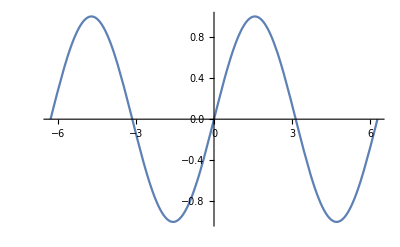

```mathematica
Plot[Sin[x],{x,-2*Pi,2*Pi}]
```

Podemos representar varias funciones a la vez :

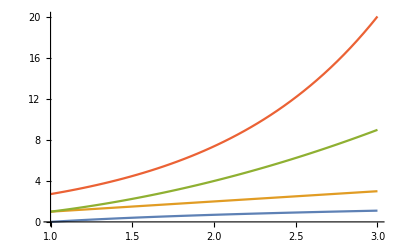

```mathematica
Plot[{Log[x],x,x^2,E^x},{x,1,3}]
```

Y podemos comparar su crecimiento usando la función Animate[] :

```mathematica
Animate[Plot[{Log[x],x,x^2,E^x},{x,1,i}],{i,3,35,.5}]
```

#### Ejemplo 2.29.

Análogamente usamos Plot3D[] para representar funciones reales de dos variables en el espacio, por ejemplo

```mathematica
Plot3D[Cos[Sqrt[x^2+y^2]],{x,-10,10},{y,-10,10},MaxRecursion->3,AspectRatio->1/2]
```

-Graphics3D-

También podemos crear animaciones como en el ejemplo anterior con la función Animate[]:

```mathematica
Animate[Plot3D[Sin[x^2+y^2+i],{x,-2,2},{y,-2,2},Mesh->Full,MaxRecursion->3],{i,0,2*Pi,.1}]
```

```mathematica
Animate[Plot3D[Sin[x^2+y^2+i],{x,-2,2},{y,-2,2},Mesh->Full,MaxRecursion->3],{i,0,2*Pi,.1}]
```

#### Ejemplo 2.30.

La función ParametricPlot[] permite representar curvas en el plano, por ejemplo:

#### Ejemplo 2.31.

Representamos un toro:

```mathematica
ParametricPlot3D[{(3+Cos[p2])*Sin[p1],(3+Cos[p2])*Cos[p1],Sin[p2]},{p1,0,2*Pi},{p2,0,2*Pi}]
```

-Graphics3D-

Y también podemos representar varias superficies u objetos:

```mathematica
GiroY[alpha_]:={{Cos[alpha],0,-Sin[alpha]},{0,1,0},{Sin[alpha],0,Cos[alpha]}};
ParametricPlot3D[Join[Table[{1.8,2,1.8}*{4*Cos[i],4,4*Sin[i]}+GiroY[i+(Pi/2)].{(3+Cos[v]) Sin[u],(3+Cos[v]) Cos[u],Sin[v]},{i,0,2*Pi,Pi/3}],Table[2*{Cos[i]*4,2.5,Sin[i]*4}+{(3+Cos[v]) Cos[u],3+Sin[v],(3+Cos[v]) Sin[u]},{i,Pi/6,2*Pi+.5,Pi/3}]],{u,0,2 Pi},{v,0,2 Pi}]
```

-Graphics3D-